```mathematica
data=Import[ToFileName[NotebookDirectory[],"newdata.csv"],"CSV"];
rawdata[[1]]
```

{Number,Name,Country,Lat,Long,Height,Jan,Feb,Mar,Apr,May,Jun,Jul,Aug,Sep,Oct,Nov,Dec}

COLUMNS: “Number”,”Name”,”Country”,”Lat”,”Long”,”Height”,”Jan”,”Feb”,”Mar”,”Apr”,”May”,”Jun”,”Jul”,”Aug”,”Sep”,”Oct”,”Nov”,”Dec”}

```mathematica
temps = data[[All,7;;18]];
```

```mathematica
pc=PrincipalComponents[temps];
```

```mathematica
Variance[pc]
```

{1156.2,195.003,6.71966,2.50697,1.42176,0.47995,0.318722,0.199693,0.106251,0.0774372,0.0553304,0.0430945}

```mathematica
twopc=pc[[All,1;;2]];
```

```mathematica
pouplation = Map[CityData[ToLowerCase[#1],"Population"]&,data[[All,2;;3]]];
```

```mathematica
labeled=Map[If[#[[3]]>1000000,
Labeled[#[[2]],#[[1]]],#[[2]]]&,
Transpose[{data[[All,2]],twopc,pouplation}]];
```

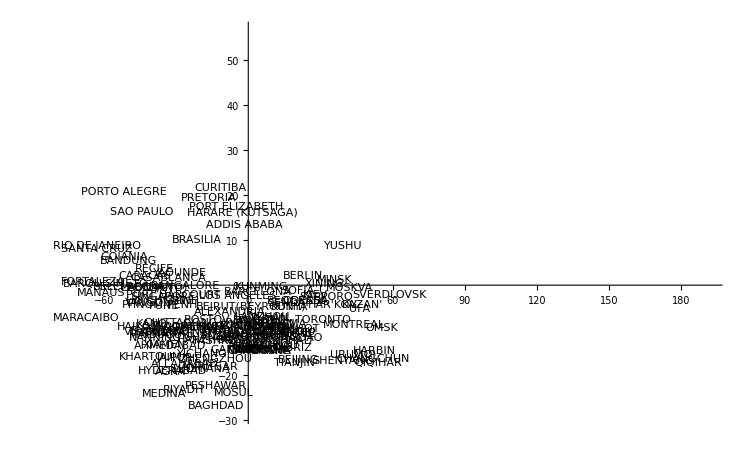

```mathematica
ListPlot[labeled]
```